#### Problem 10.6.12c

```mathematica
fx0[x_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*0]*Cos[2*n*Pi*x/40],{n,1,50}]
```

```mathematica
fx1[x_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*1]*Cos[2*n*Pi*x/40],{n,1,50}]
```

```mathematica
fx2[x_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*2]*Cos[2*n*Pi*x/40],{n,1,50}]
```

```mathematica
fx3[x_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*3]*Cos[2*n*Pi*x/40],{n,1,50}]
```

```mathematica
fx5[x_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*5]*Cos[2*n*Pi*x/40],{n,1,50}]
```

```mathematica
fx8[x_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*8]*Cos[2*n*Pi*x/40],{n,1,50}]
```

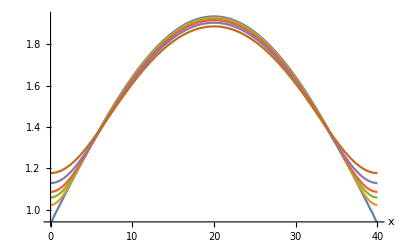

```mathematica
Plot[{fx0[x],fx1[x],fx2[x],fx3[x],fx5[x],fx8[x]},{x,0,40}, AxesLabel->Automatic]
```

```mathematica
ft0[t_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*0/40],{n,1,50}]
```

```mathematica
ft1[t_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*8/40],{n,1,50}]
```

```mathematica
ft2[t_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*16/40],{n,1,50}]
```

```mathematica
ft3[t_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*24/40],{n,1,50}]
```

```mathematica
ft4[t_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*32/40],{n,1,50}]
```

```mathematica
ft5[t_]:=(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*40/40],{n,1,50}]
```

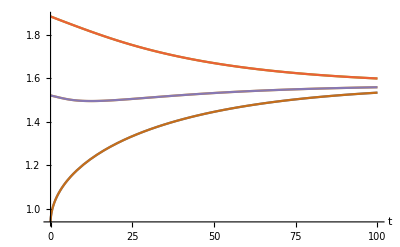

```mathematica
Plot[{ft0[t],ft1[t],ft2[t],ft3[t],ft4[t],ft5[t]},{t,0,100}, AxesLabel->Automatic]
```

```mathematica
Plot3D[(Pi/2)+Sum[((2+2*Cos[Pi*2*n])/(Pi*(1-((2*n)^2))))*Exp[(-1)*((2*n*Pi/40)^2)*t]*Cos[2*n*Pi*x/40],{n,1,50}], {x,0,40},{t,0,60}, AxesLabel->Automatic, PlotRange->Full]
```

-Graphics3D-

```mathematica
(1/L) Integrate[Sin[Pi*x/L]*Cos[Pi*x*n/L],{x,0,L}]
```

(1+Cos[n π])/(π-n^2 π)

#### Problem 10.7.4bc

```mathematica
g[x_,t_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*t/10]*Sin[n*Pi*x/10], {n,1,50}]
```

```mathematica
gx1[x_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*1/10]*Sin[n*Pi*x/10], {n,1,50}]
```

```mathematica
gx2[x_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*2/10]*Sin[n*Pi*x/10], {n,1,50}]
```

```mathematica
gx3[x_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*3/10]*Sin[n*Pi*x/10], {n,1,50}]
```

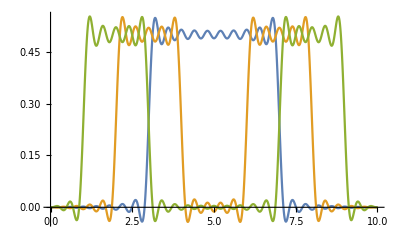

```mathematica
Plot[{gx1[x],gx2[x],gx3[x]},{x,0,10}, PlotRange->Full]
```

```mathematica
gt1[1_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*t/10]*Sin[n*Pi*1/10], {n,1,50}]
```

```mathematica
gt2[1_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*t/10]*Sin[n*Pi*2/10], {n,1,50}]
```

```mathematica
gt3[1_]:=Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*t/10]*Sin[n*Pi*3/10], {n,1,50}]
```

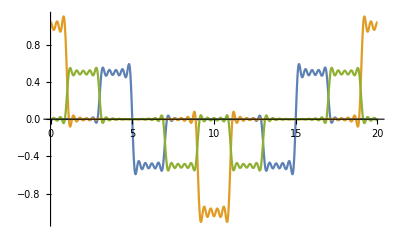

```mathematica
Plot[{gt1[t],gt2[t],gt3[t]},{t,0,20}, PlotRange-> Full]
```

```mathematica
Plot3D[Sum[(4/(n*Pi))*Sin[n*Pi/2]*Sin[n*Pi/10]*Cos[n*Pi*t/10]*Sin[n*Pi*x/10], {n,1,50}], {x,0,10},{t,0,20}, AxesLabel->Automatic]
```

-Graphics3D-